```mathematica
t=NDSolve[{y'[x]==y[x] x,y[1]==1},y,{x,1,5}]
```

{{y→InterpolatingFunction[…]}}

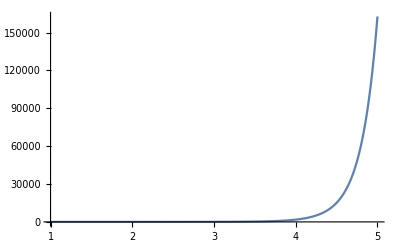

```mathematica
Plot[Evaluate[y[x]/. t],{x,1,5},PlotRange->All]
```

```mathematica
s=NDSolve[{y'[x]==y[x] Cos[x+y[x]],y[0]==1},y,{x,0,10}]
```

{{y→InterpolatingFunction[…]}}

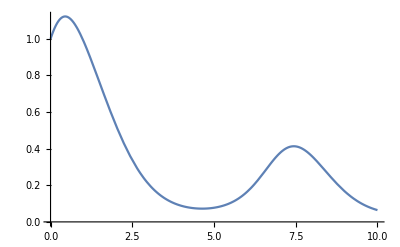

```mathematica
Plot[Evaluate[y[x]/. s],{x,0,10}]
```